# Median Filter Tests for Dominik

To clarify my image of how to proceed in week of 2015.10 .12

## Plot filter results

```mathematica
(*Example use of Partition[] function*)
Partition[Range[10], 5, 1]
```

{{1,2,3,4,5},{2,3,4,5,6},{3,4,5,6,7},{4,5,6,7,8},{5,6,7,8,9},{6,7,8,9,10}}

```mathematica
(*Simple and inefficient implementation of median filter*)
(*Actually, the median filter will only really work for odd window lengths.*)
slidingMedian[data_List, windowLength_/;OddQ[windowLength]]:= Median /@ Partition[data, windowLength, 1];

sinWaveMedianFilterPlottingData[oneCycleLength_, windowLength_/;OddQ[windowLength]]:=
Module[{data,delayPoints,tempData, slidingMedianData},

data=Table[N[Sin[x/oneCycleLength* 2 Pi]], {x, 0, oneCycleLength*10}];
delayPoints=Floor[windowLength/2];
slidingMedianData = slidingMedian[data, windowLength];

(*Cut partial cycle at beginning and end of sliding Median data to compensate for delays. Mathematica indexing starts at one! *)
slidingMedianData = 
slidingMedianData[[(oneCycleLength-delayPoints)+1;;  - oneCycleLength + delayPoints-1 ]];
(*Cut off first cycle from original data*)
tempData=data[[  oneCycleLength + 1 ;;oneCycleLength + Length[slidingMedianData] ]];  

(*return the cut original data, the cut sliding median data, and the median filtered result*)
{tempData, slidingMedianData, tempData-slidingMedianData}
];
```

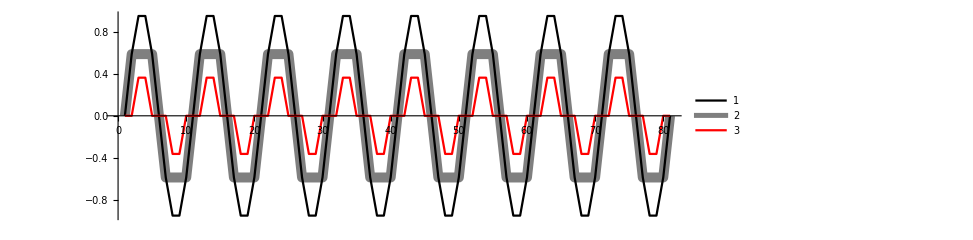

```mathematica
ListLinePlot[sinWaveMedianFilterPlottingData[10, 5], AspectRatio->1/3, ImageSize->72*10, PlotLegends->Automatic, PlotStyle->{Directive[Black,Thin],Directive[Thickness[0.01], Opacity[0.5, Black]], Directive[Red]}]
```

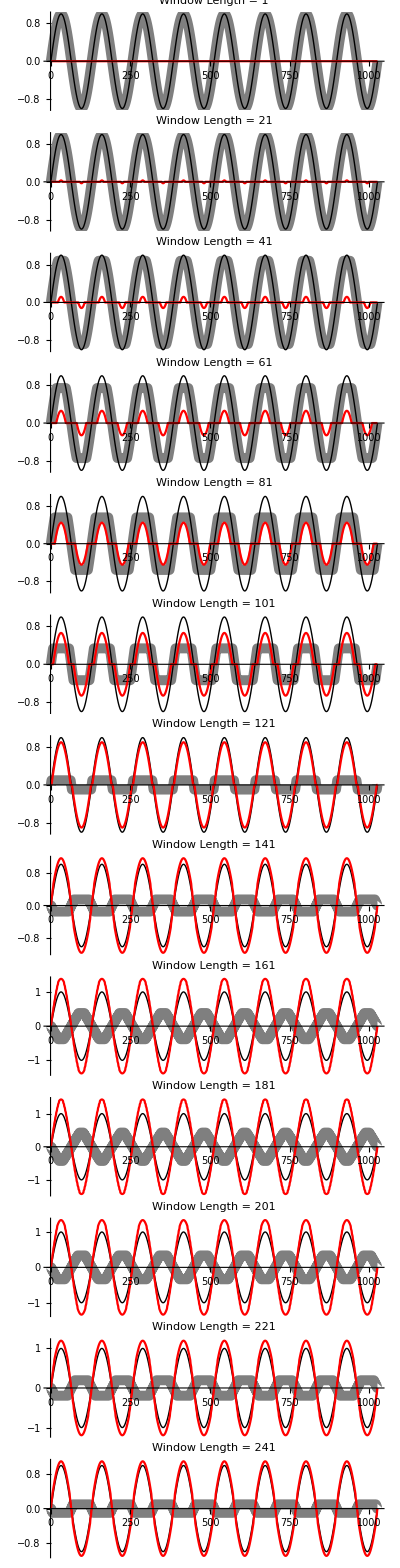

```mathematica
Table[
ListLinePlot[sinWaveMedianFilterPlottingData[128, wl], PlotLabel->"Window Length = "<>ToString[wl],AspectRatio->1/5, ImageSize->72*10, PlotStyle->{Directive[Black,Thin],Directive[Thickness[0.01], Opacity[0.5, Black]], Directive[Red]}],
{wl, 1, 256, 20}] //TableForm
```

## Plot Filter Trends

```mathematica
originalVsFiltered=Table[ sinWaveMedianFilterPlottingData[128, wl][[{1, 3}]],
{wl, 1, 256,2}];
```

```mathematica
Dimensions[ originalVsFiltered ]
```

{128,2,1025}

```mathematica
rmsRatio[ {data_, filteredData_}]:=RootMeanSquare[filteredData]/RootMeanSquare[data]
```

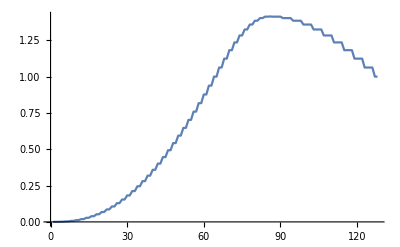

```mathematica
ListLinePlot[ rmsRatio /@ originalVsFiltered ]
```

```mathematica
absMeanRatio[ {data_, filteredData_}]:=Mean[Abs[filteredData]]/Mean[Abs[data]]
```

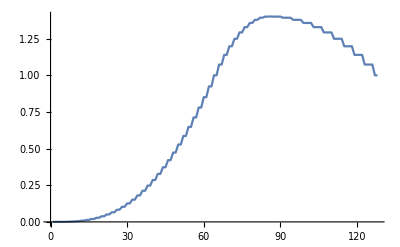

```mathematica
ListLinePlot[ absMeanRatio /@ originalVsFiltered ]
```

```mathematica
singlePointRatioMean[ {data_, filteredData_}]:=Mean[filteredData/data]
```

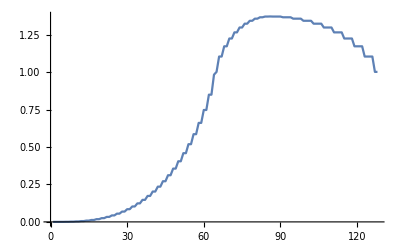

```mathematica
ListLinePlot[ singlePointRatioMean /@ originalVsFiltered ]
```